```mathematica
SetDirectory[NotebookDirectory[]]
```

```mathematica
rawdata = Import["DataForPlotting\\Fig4B_data.txt","Table"];
```

```mathematica
Dimensions[rawdata]
```

{27520,2}

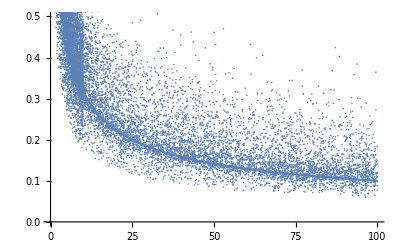

```mathematica
Show[ListPlot[rawdata,PlotRange->{{0,100},{0,0.5}}],Plot[Sqrt[1/x],{x,0,100}]]
```

```mathematica
theaddingfunction[x_,dat_]:=Module[{t=RandomSample[dat,1][[1]]},If[Length[Nearest[x,t,{Infinity,.01}]]<2,Prepend[x,t],x]]
```

```mathematica
rescaleddata = Table[{rawdata[[n]][[1]]*0.5/100,rawdata[[n]][[2]]},{n,1,Dimensions[rawdata][[1]]}];
```

```mathematica
Clear[densADJ];
densADJ=RandomSample[rescaleddata,1]
```

{{0.404658,0.122105}}

```mathematica
Do[densADJ=theaddingfunction[densADJ,rescaleddata],{n,1,25000}];
```

```mathematica
Dimensions[densADJ]
```

{2481,2}

```mathematica
densADJrescaled = Table[{densADJ[[n]][[1]]*100/0.5,densADJ[[n]][[2]]},{n,1,Dimensions[densADJ][[1]]}];
```

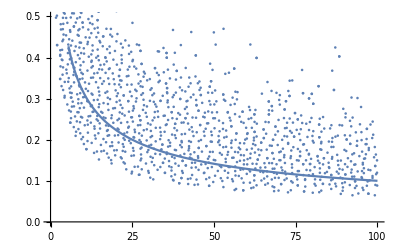

```mathematica
Show[ListPlot[densADJrescaled,PlotRange->{{0,100},{0,0.5}}],Plot[Sqrt[1/x],{x,0,100}]]
```

```mathematica
Export["DataForPlotting\\Fig4B_densADJ.txt",densADJrescaled, "Table"]
```